# Ramsey’s Theorem

Ramsey’s theorem states that for any complete graph, there exists some number such that any edge 2-coloring yields a complete subgraph of that size in one of the colors, or informally, “complete disorder is impossible.”

## Friends and Strangers

We begin by looking a famous special case of Ramsey’s theorem, the theorem on friends and strangers, which states that in a group of six people, either three people mutually know each other, or three people mutually do not know each other.

Make a complete graph with 6 vertices

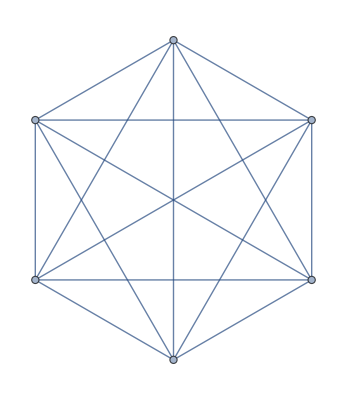

```mathematica
CompleteGraph[6]
```

The theorem begins with six people at a party, so we label each vertex to represent person.

Label vertices on the graph

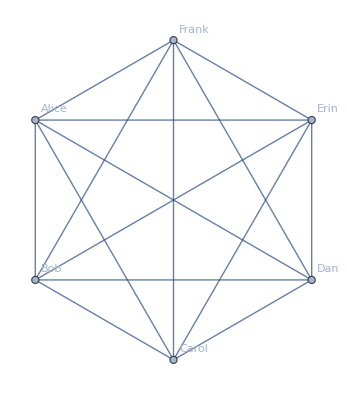

```mathematica
CompleteGraph[6, VertexLabels->{1->Alice,2->Bob,3->Carol,4->Dan,5->Erin,6->Frank}]
```

Now assume these people are either mutually friends or strangers. We can use two colors to represent the relations.

Color edges on the graph

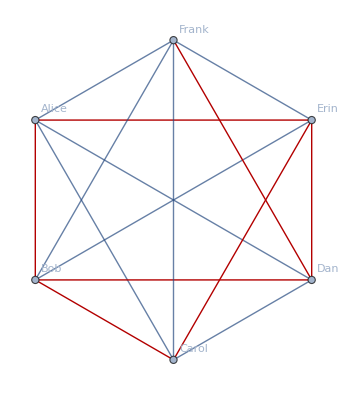

```mathematica
HighlightGraph[CompleteGraph[6,VertexLabels->{1->Alice,2->Bob,3->Carol,4->Dan,5->Erin,6->Frank}],{1<->2,1<->5,2<->3,2<->4,3<->5,4<->5,4<->6}]
```

A blue edge means two people are friends while a red edge means they are strangers. Now let us separate the two graphs.

Draw the subgraph with only the red edges

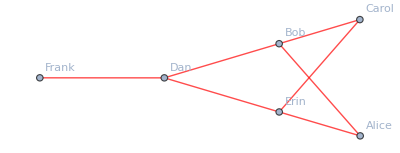

```mathematica
Graph[{1<->2,1<->5,2<->3,2<->4,3<->5,4<->5,4<->6},VertexLabels->{1->Alice,2->Bob,3->Carol,4->Dan,5->Erin,6->Frank},EdgeStyle->Red]
```

Draw the complete graph with the red edges removed

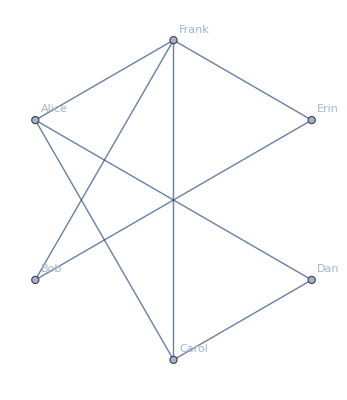

```mathematica
EdgeDelete[CompleteGraph[6,VertexLabels->{1->Alice,2->Bob,3->Carol,4->Dan,5->Erin,6->Frank}],{1<->2,1<->5,2<->3,2<->4,3<->5,4<->5,4<->6}]
```

We first check the red subgraph for complete subgraphs with 3 vertices.

Find any cliques of at least 3 vertices in the red subgraph

```mathematica
FindClique[Graph[{1<->2,1<->5,2<->3,2<->4,3<->5,4<->5,4<->6}],{3, 6}]
```

{}

The theorem on friends and strangers tells us that since the red subgraph has no complete subgraphs of size 3, then the blue subgraph must.

Find any cliques of at least 3 vertices in the blue subgraph

```mathematica
FindClique[EdgeDelete[CompleteGraph[6],{1<->2,1<->5,2<->3,2<->4,3<->5,4<->5,4<->6}],{3, 6}]
```

{{1,3,6}}

Highlight the clique with thick edges

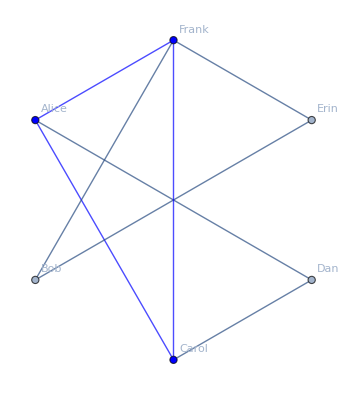

```mathematica
HighlightGraph[-Graphics-,Style[Subgraph[-Graphics-,FindClique[EdgeDelete[CompleteGraph[6],{1<->2,1<->5,2<->3,2<->4,3<->5,4<->5,4<->6}],{3, 6}]],{Blue, Thick}]]
```

Display the 2-colored complete graph and highlight the clique with thick edges

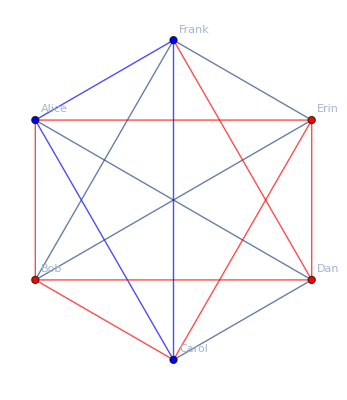

```mathematica
HighlightGraph[-Graphics-,{Style[-Graphics-,{Red}],Style[Subgraph[-Graphics-,FindClique[EdgeDelete[CompleteGraph[6],{1<->2,1<->5,2<->3,2<->4,3<->5,4<->5,4<->6}],{3, 6}]],{Blue,Thick}]}]
```

We can try some more examples. Since any 2-coloring will work, we can randomly select an edge set from the graph to represent the other color.

Choose a random edge subset from the complete graph

```mathematica
RandomChoice[Subsets[EdgeList[CompleteGraph[6]]]]
```

{1<->4,1<->5,2<->3,2<->6,4<->5}

Display the 2-colored complete graph and highlight cliques of either color with thick edges

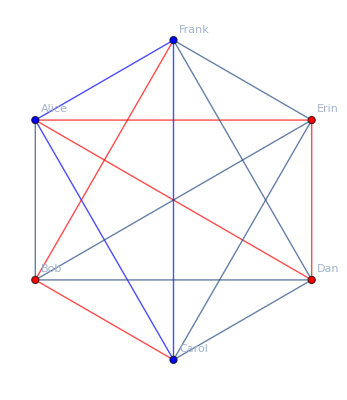

```mathematica
HighlightGraph[-Graphics-,{Style[Graph[%],{Red}],Style[Subgraph[Graph[%],FindClique[Graph[%],{3, 6}]],{Red,Thick}],Style[Subgraph[EdgeDelete[-Graphics-,%],FindClique[EdgeDelete[-Graphics-,%],{3, 6}]],{Blue,Thick}]}]
```

Define a function to display the 2-colored complete graph and highlight cliques of either color with thick edges

```mathematica
f[s_]:=HighlightGraph[-Graphics-,{Style[Graph[s],{Red}],Style[Subgraph[Graph[s],FindClique[Graph[s],{3, 6}]],{Red,Thick}],Style[Subgraph[EdgeDelete[-Graphics-,s],FindClique[EdgeDelete[-Graphics-,s],{3, 6}]],{Blue,Thick}]}]
```

Apply the function to thirty random edge subsets

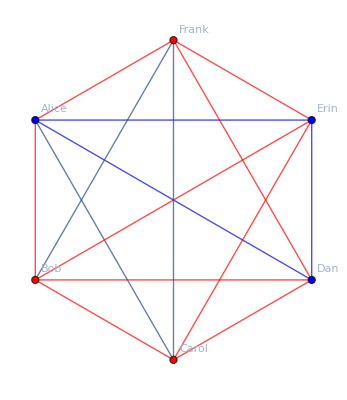
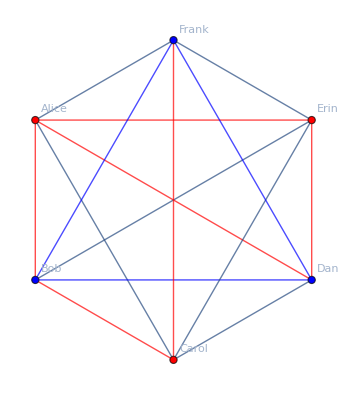
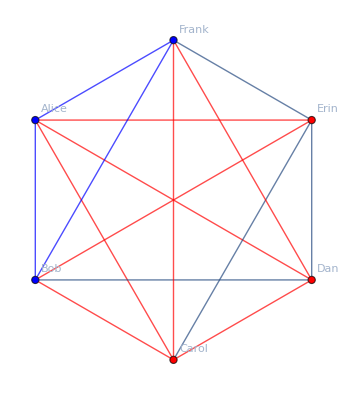
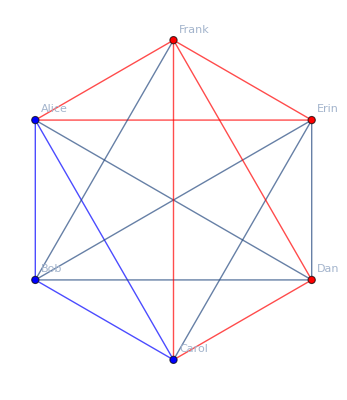
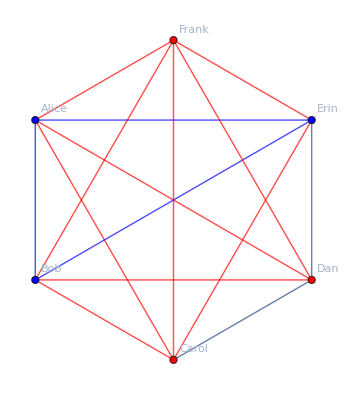
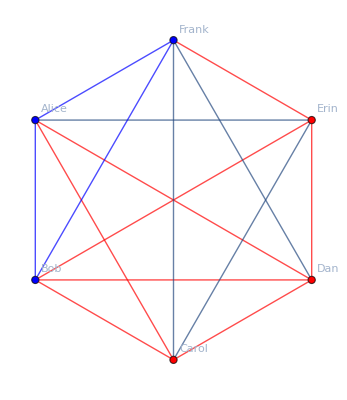
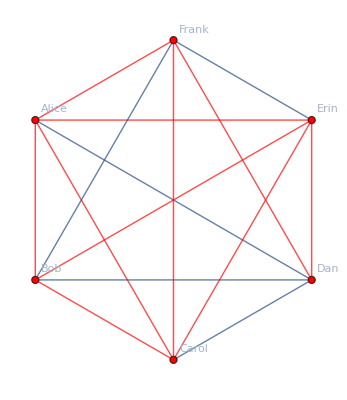
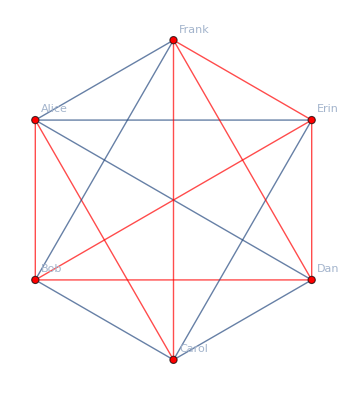

```mathematica
Map[f,RandomSample[Subsets[EdgeList[CompleteGraph[6]]],30]]
```

## Ramsey Numbers

But what happens if we use a complete graph of 5 vertices instead of 6?

Define a function that draws the 2-colored complete graph of 5 vertices whenever there is no clique of at least 3 vertices in either color

```mathematica
f[s_]:=If[Length[Union[FindClique[Graph[s],{3, 5}],FindClique[EdgeDelete[CompleteGraph[5],s],{3, 5}]]]==0,HighlightGraph[CompleteGraph[5],s],##&[]]
```

We can do an exhaustive search on all possible 2-colorings.

Apply the function to all edge subsets of the complete graph of 5 vertices

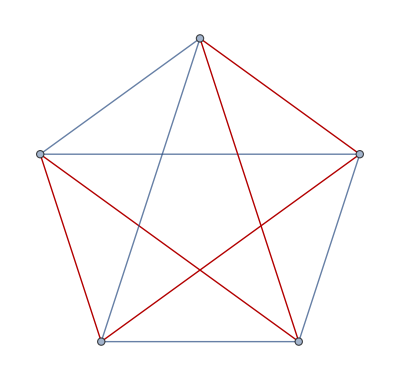
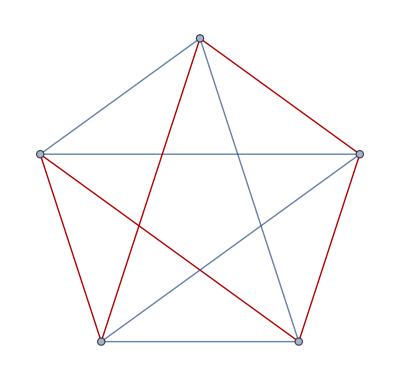
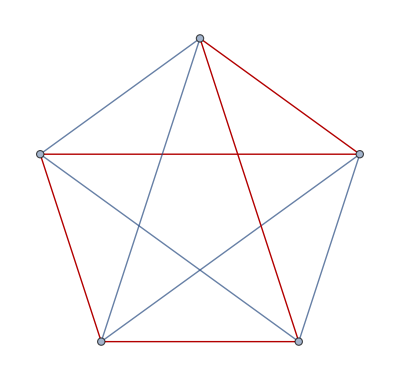
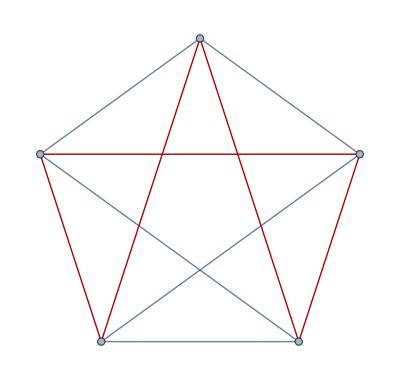
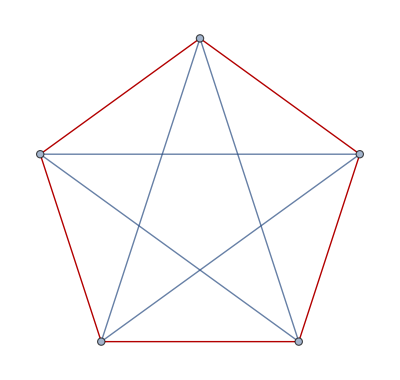
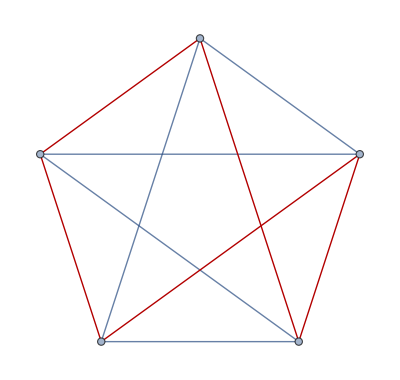
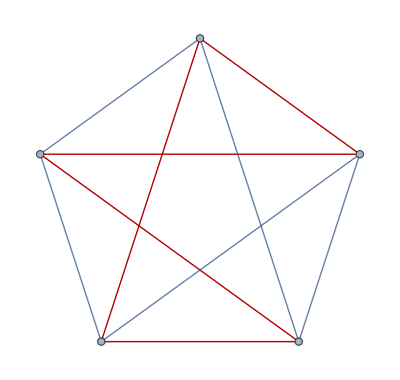
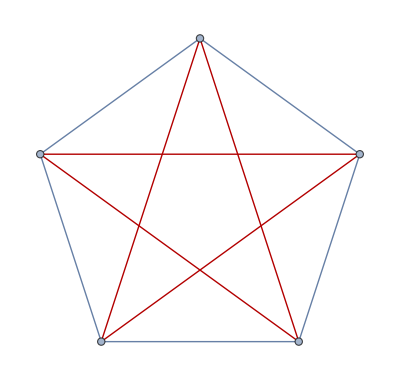

```mathematica
Map[f,Subsets[EdgeList[CompleteGraph[5]]]]
```

So we have a total of 12 counterexamples when the complete graph has only 5 vertices. We can modify the function and run the same exhaustive check on complete graphs of 6 vertices.

Define a function that draws the 2-colored complete graph of 6 vertices whenever there is no clique of at least 3 vertices in either color

```mathematica
f[s_]:=If[Length[Union[FindClique[Graph[s],{3, 6}],FindClique[EdgeDelete[CompleteGraph[6],s],{3, 6}]]]==0,HighlightGraph[CompleteGraph[6],s],##&[]]
```

Apply the function to all edge subsets of the complete graph of 6 vertices

```mathematica
Map[f,Subsets[EdgeList[CompleteGraph[6]]]]
```

{}

Since the result set is empty, this proves the theorem on friends and strangers, which we can restate as R(3, 3) = 6. This means: if we want a complete graph that for any 2-coloring always has either [1] a clique of size 3 in the first color, or [2] a clique of size 3 in the second color, then we must have at least 6 vertices.

We know that R(4, 4) = 18, so here is a counterexample showing that R(4, 4) cannot be 17.

Define a function that draws the 2-colored complete graph of 17 vertices whenever there is no clique of at least 4 vertices in either color, and also draws the colored components individually

```mathematica
f[s_]:=If[Length[Union[FindClique[Graph[s],{4, 17}],FindClique[EdgeDelete[CompleteGraph[17],s],{4, 17}]]]==0,{HighlightGraph[CompleteGraph[17],s],HighlightGraph[CompleteGraph[17],Graph[s],EdgeStyle->Red,GraphHighlightStyle->{"DehighlightHide"}],HighlightGraph[CompleteGraph[17],EdgeDelete[CompleteGraph[17],s],GraphHighlightStyle->{"DehighlightHide"}]},##&[]]
```

Construct a set of all edges on the complete graph of size 17 that are distance 1, 2, 4, or 8 from each other

```mathematica
Union[Table[i<->17-Mod[17-(i+1), 17],{i,17}],Table[i<->17-Mod[17-(i+2),17],{i,17}],Table[i<->17-Mod[17-(i+4),17],{i,17}],Table[i<->17-Mod[17-(i+8),17],{i,17}]]
```

{1<->2,1<->3,1<->5,1<->9,2<->3,2<->4,2<->6,2<->10,3<->4,3<->5,3<->7,3<->11,4<->5,4<->6,4<->8,4<->12,5<->6,5<->7,5<->9,5<->13,6<->7,6<->8,6<->10,6<->14,7<->8,7<->9,7<->11,7<->15,8<->9,8<->10,8<->12,8<->16,9<->10,9<->11,9<->13,9<->17,10<->1,10<->11,10<->12,10<->14,11<->2,11<->12,11<->13,11<->15,12<->3,12<->13,12<->14,12<->16,13<->4,13<->14,13<->15,13<->17,14<->1,14<->5,14<->15,14<->16,15<->2,15<->6,15<->16,15<->17,16<->1,16<->3,16<->7,16<->17,17<->1,17<->2,17<->4,17<->8}

Test the counterexample

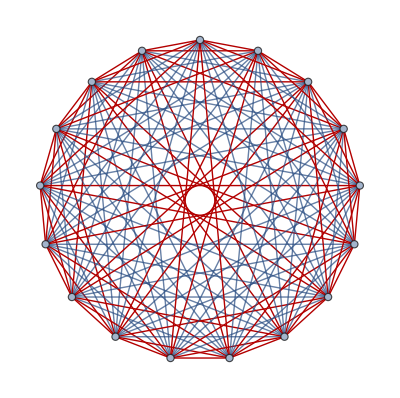
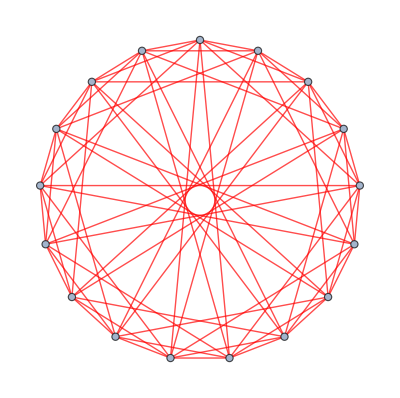
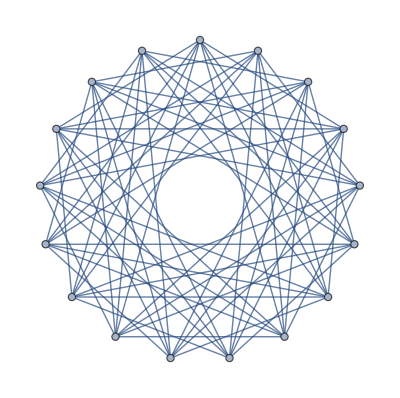

```mathematica
f[%]
```

For comparison, here are some examples of 2-colored complete graphs of 18 vertices, all of which will have a clique of size 4 in at least one color.

Define a function that draws the 2-colored complete graph of 18 vertices and highlight cliques of size 4 in either color with thick edges

```mathematica
f[s_]:=HighlightGraph[CompleteGraph[18],{Style[Graph[s],{Red}],Style[Subgraph[Graph[s],FindClique[Graph[s],{4, 18}]],{Red,Thick}],Style[Subgraph[EdgeDelete[CompleteGraph[18],s],FindClique[EdgeDelete[CompleteGraph[18],s],{4, 18}]],{Blue,Thick}]}]
```

Define a filter that takes an edge set and drops each edge with probability 1/2

```mathematica
g[s_]:=If[RandomInteger[]==1,s,##&[]]
```

Apply the function to one filtered edge set and magnify the picture by a factor of 3

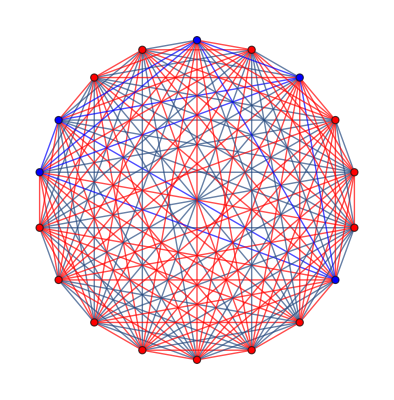

```mathematica
Magnify[f[Map[g,EdgeList[CompleteGraph[18]]]],3]
```

Apply the function to thirty filtered edge subsets

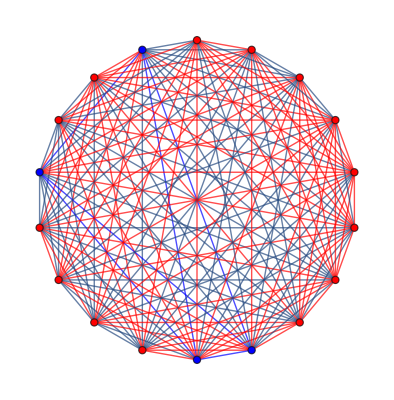
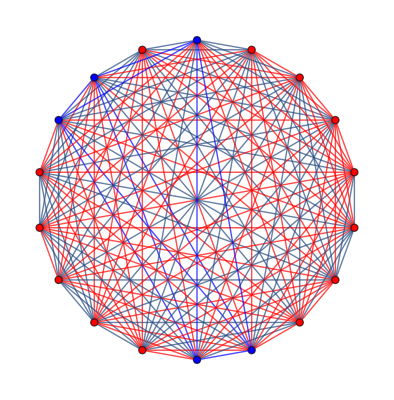
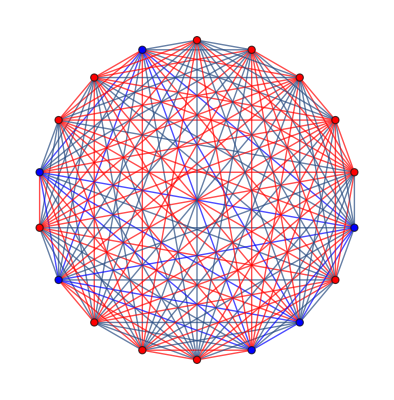
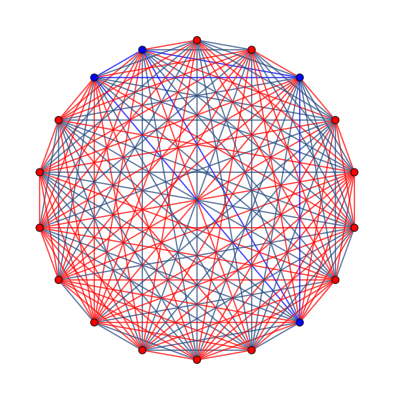
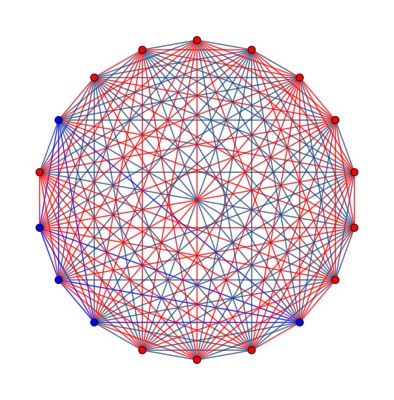
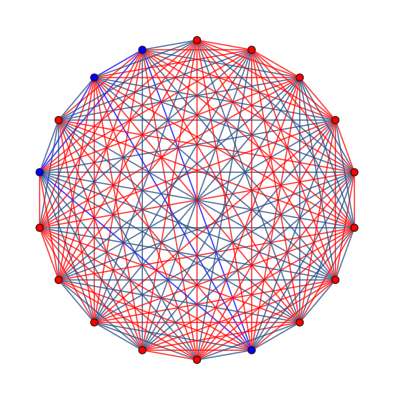
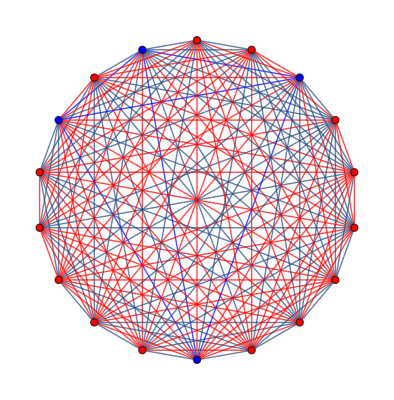
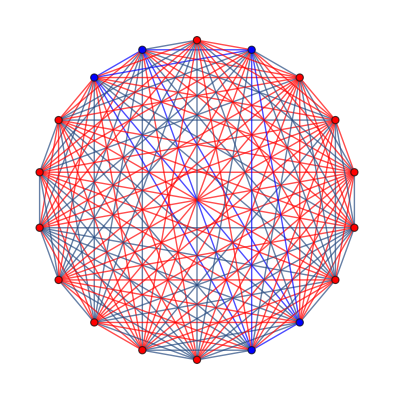

```mathematica
Map[f,Table[Map[g,EdgeList[CompleteGraph[18]]],{30}]]
```

R(5, 5) is still unknown, although we currently know it is at least 43. Here is an example of a random 2-coloring on a complete graph of size 42 with the cliques of size 5 highlighted.

Define a function that draws the 2-colored complete graph of 42 vertices and highlight cliques of size 5 in either color with thick edges

```mathematica
f[s_]:=HighlightGraph[CompleteGraph[42],{Style[Graph[s],{Red}],Style[Subgraph[Graph[s],FindClique[Graph[s],{5, 42}]],{Red,Thick}],Style[Subgraph[EdgeDelete[CompleteGraph[42],s],FindClique[EdgeDelete[CompleteGraph[42],s],{5, 42}]],{Blue,Thick}]}]
```

Apply the function to one filtered edge set and magnify the picture by a factor of 3

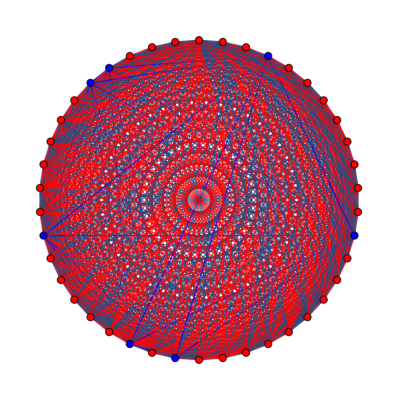

```mathematica
Magnify[f[Map[g,EdgeList[CompleteGraph[42]]]],3]
```

## Non-Diagonal Ramsey Numbers

We can generalize this to the non-diagonal case where the two parameters are different, meaning we require the cliques to be different sizes for each color. We know that R(3, 4) = 9, so here is a counterexample showing that R(3, 4) cannot be 8.

Define a function that draws the 2-colored complete graph of 8 vertices whenever there is no clique of 3 vertices in one color and no clique of 4 vertices in the other, and also draws the colored components individually

```mathematica
f[s_]:=If[Length[Union[FindClique[Graph[s],{3, 8}],FindClique[EdgeDelete[CompleteGraph[8],s],{4, 8}]]]==0,{HighlightGraph[CompleteGraph[8],s],HighlightGraph[CompleteGraph[8],Graph[s],EdgeStyle->Red,GraphHighlightStyle->{"DehighlightHide"}],HighlightGraph[CompleteGraph[8],EdgeDelete[CompleteGraph[8],s],GraphHighlightStyle->{"DehighlightHide"}]},##&[]]
```

Construct a set of all edges on the complete graph of size 8 that are distance 1 or 4 from each other, removing duplicate edges

```mathematica
Union[Table[i<->8-Mod[8-(i+1), 8],{i,8}],Table[i<->8-Mod[8-(i+4),8],{i,8}]]
```

{1<->2,1<->5,2<->3,2<->6,3<->4,3<->7,4<->5,4<->8,5<->1,5<->6,6<->2,6<->7,7<->3,7<->8,8<->1,8<->4}

Remove duplicate edges

```mathematica
DeleteDuplicates[Sort /@%]
```

{1<->2,1<->5,2<->3,2<->6,3<->4,3<->7,4<->5,4<->8,5<->6,6<->7,7<->8,1<->8}

Test the counterexample

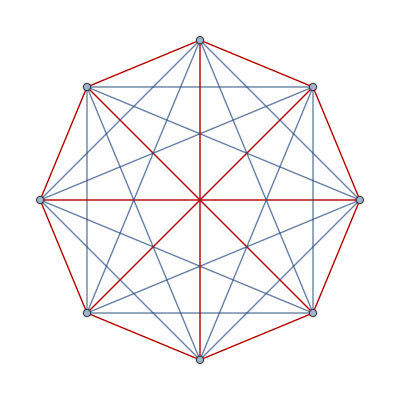
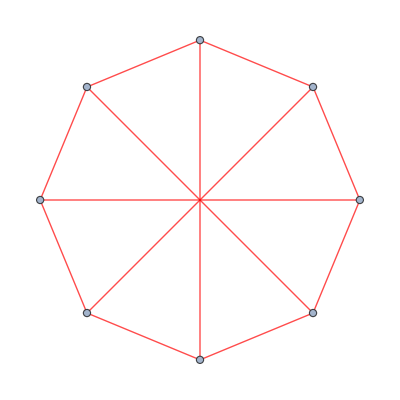
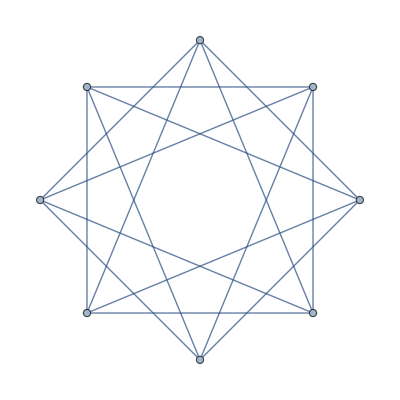

```mathematica
f[%]
```

For comparison, here are some examples of 2-colored complete graphs of 9 vertices, all of which will have a clique of size 3 in red or a clique of size 4 in blue.

Define a function that draws the 2-colored complete graph of 18 vertices and highlight red cliques of size 3 and blue cliques of size 4 with thick edges

```mathematica
f[s_]:=HighlightGraph[CompleteGraph[9],{Style[Graph[s],{Red}],Style[Subgraph[Graph[s],FindClique[Graph[s],{3, 9}]],{Red,Thick}],Style[Subgraph[EdgeDelete[CompleteGraph[9],s],FindClique[EdgeDelete[CompleteGraph[9],s],{4, 9}]],{Blue,Thick}]}]
```

Apply the function to 30 filtered edges

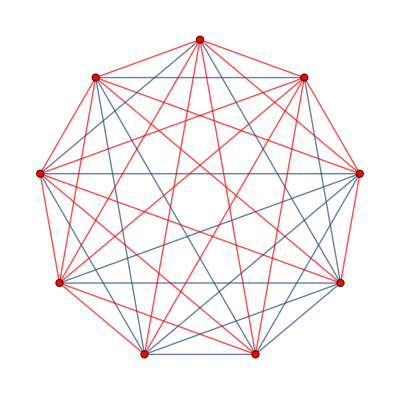
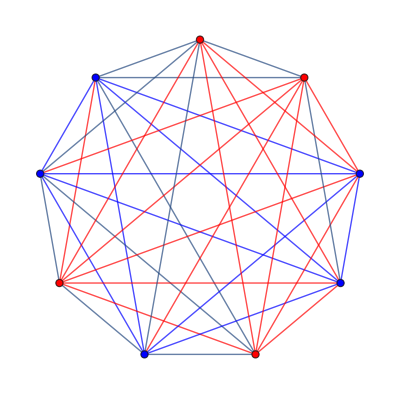
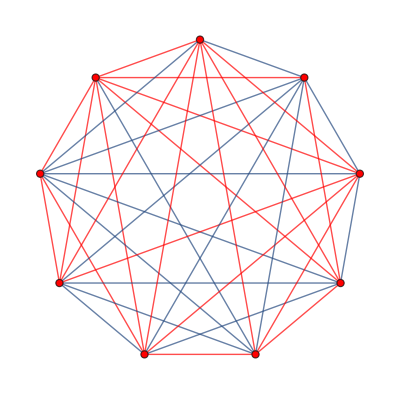
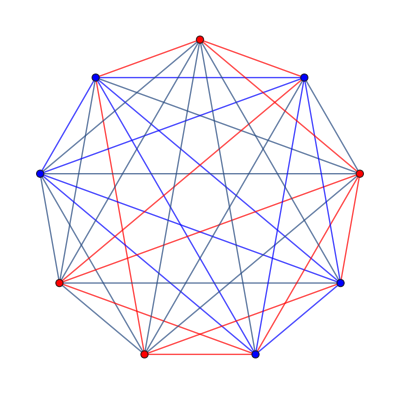
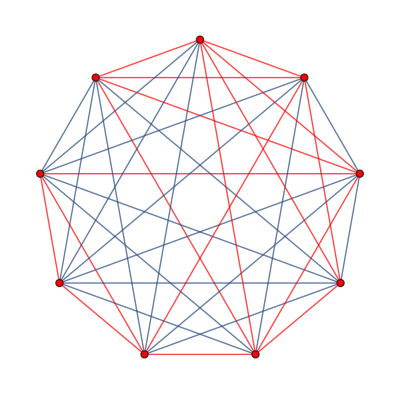
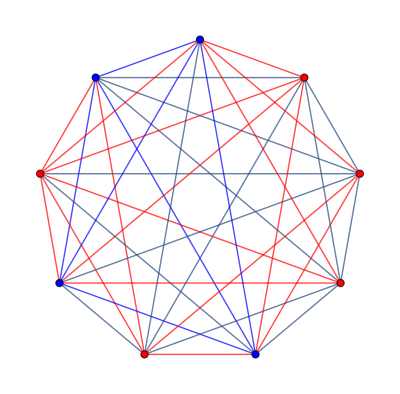
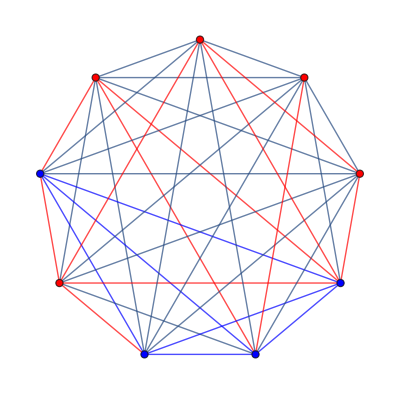
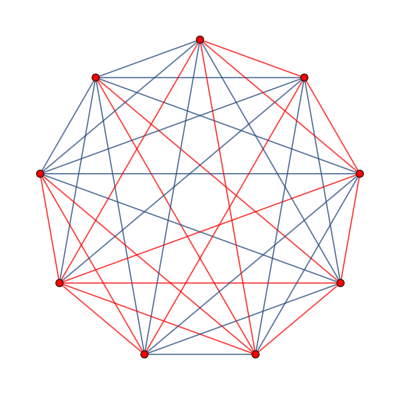
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[f,Table[Map[g,EdgeList[CompleteGraph[9]]],{30}]]
```

Further Explorations

Generalized and Hypergraph Ramsey Numbers
Schur Numbers
Distributed Computing in Case of Alien Invasion

Authorship information

Dennis Hou

6/21/2017

smilax@gmail.com